```mathematica
RCon[x_,y_]:=1/2(x+y-Sqrt[(x-y)^2])
RDiz[x_,y_]:=1/2(x+y+Sqrt[(x-y)^2])
```

```mathematica
f1[x_,y_]:=1-x^2
f2[x_,y_]:=1-y^2
f12[x_,y_]:=RCon[f1[x,y],f2[x,y]]
f12m[x_,y_]:=If[f12[x,y]<0,0,f12[x,y]]
f12m2[x_,y_]:=Tanh[5f12m[x,y]]
```

```mathematica
Plot3D[f12m2[x,y],{x,-2,2},{y,-2,2},PlotRange->Full]
```

-Graphics3D-

```mathematica
f3[x_,y_]:=x
f4[x_,y_]:=y
f34[x_,y_]:=RCon[f3[x,y],f4[x,y]]
(*f34m[x_,y_]:=If[f34[x,y]<0,0,f34[x,y]]
f34m2[x_,y_]:=Tanh[5f34m[x,y]]*)
```

```mathematica
Plot3D[f34[x,y],{x,0,1},{y,0,1},PlotRange->Full]
```

-Graphics3D-

```mathematica
f5[x_,y_]:=1-x
f6[x_,y_]:=1-y
f56[x_,y_]:=RCon[f5[x,y],f6[x,y]]
(*f56m[x_,y_]:=If[f56[x,y]<0,0,f56[x,y]]
f56m2[x_,y_]:=Tanh[5f56m[x,y]]*)
```

```mathematica
Plot3D[f56[x,y],{x,0,1},{y,0,1},PlotRange->Full]
```

-Graphics3D-

```mathematica
f3456[x_,y_]:=f56[x,y]/(f34[x,y]+f56[x,y])
```

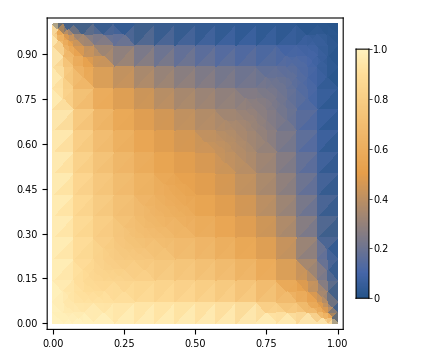
-Graphics3D--Graphics-

```mathematica
Row[{
Plot3D[f3456[x,y],{x,0,1},{y,0,1},PlotRange->Full,ImageSize->Medium],
DensityPlot[f3456[x,y],{x,0,1},{y,0,1},PlotRange->Full,PlotLegends->Automatic,ImageSize->Medium]}]
```

```mathematica
-Graphics3D--Graphics-
```

-Graphics3D--Graphics-

```mathematica
f7[x_,y_]:=0.25-x^2
f8[x_,y_]:=0.25-y^2
f78[x_,y_]:=RCon[f7[x,y],f8[x,y]]
```

```mathematica
Plot3D[f78[x,y],{x,-0.5,0.5},{y,-0.5,0.5}]
```

-Graphics3D-

```mathematica
{fx,fy}=Grad[f3456[x,y],{x,y}]
```

{-((2-x-y-√((-x+y)^2)) (1/2 (1-(x-y)/(√((x-y)^2)))+1/2 (-1+(-x+y)/(√((-x+y)^2)))))/(2 (1/2 (x-√((x-y)^2)+y)+1/2 (2-x-y-√((-x+y)^2)))^2)+(-1+(-x+y)/(√((-x+y)^2)))/(2 (1/2 (x-√((x-y)^2)+y)+1/2 (2-x-y-√((-x+y)^2)))),-((2-x-y-√((-x+y)^2)) (1/2 (1+(x-y)/(√((x-y)^2)))+1/2 (-1-(-x+y)/(√((-x+y)^2)))))/(2 (1/2 (x-√((x-y)^2)+y)+1/2 (2-x-y-√((-x+y)^2)))^2)+(-1-(-x+y)/(√((-x+y)^2)))/(2 (1/2 (x-√((x-y)^2)+y)+1/2 (2-x-y-√((-x+y)^2))))}

```mathematica
Plot3D[{fx,fy},{x,0,1},{y,0,1},PlotRange->Full]
```

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics3D-